```mathematica
Clear[h]
```

```mathematica
(* metric *)
(* coordinates r,theta grid*)

cx0=KSx0==x0;
cx3=KSx3==x3;
cx1=KSx1==Exp[x1];
(*cx2=KSx2==(Tan[H0 Pi ((x2+(MY1+(2(MY2-MY1))/Exp[x1])(1-2x2))-1/2)]/Tan[H0 Pi/2 ]+1)Pi/2;*)
cx2=KSx2==(x2+(MY1+(2(MY2-MY1))/Exp[x1])(1-2x2))Pi;
suborg={cx0[[1]]->cx0[[2]],cx1[[1]]->cx1[[2]],cx2[[1]]->cx2[[2]],cx3[[1]]->cx3[[2]]}
R00=0;Rin=1.65;Rout=10000; NX=100;H00=0.6;NY=100;miny=0.01;miny2=0.1;
grid=Table[{cx2[[2]]-π/2,cx1[[2]]}/.{R0->R00,H0->H00,MY1->miny,MY2->miny2},{x1,Log[Rin-R00],Log[Rout-R00],(Log[Rout-R00]-Log[Rin-R00])/NX},{x2,0,1,1/NY}];
```

{KSx0→x0,KSx1→ⅇ^x1,KSx2→π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2),KSx3→x3}

```mathematica
fth[miny_,miny2_]:=miny+(2(miny2-miny))/x
```

```mathematica
Plot[{fth[1,3],fth[1,2]},{x,2,100},PlotRange->All];
```

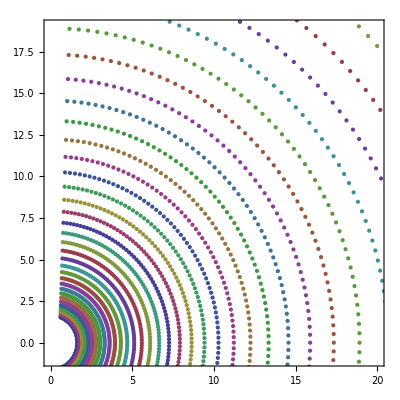

```mathematica
ListPolarPlot[grid,Frame->True,PlotRange->{{0,20},{-1,19}}]
```

```mathematica
cx2/.{ⅇ^x1+R0->KSx1}
cx2/.icx1
```

KSx2==π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)

KSx2==π ((MY1+(2 (-MY1+MY2))/(KSx1-R0)) (1-2 x2)+x2)

```mathematica
(* inverse transformation *)
subinv={
icx0=Solve[cx0,x0][[1,1]],
icx1=x1->Log[KSx1],
icx2=Solve[cx2/.icx1,x2][[1,1]],
icx3=Solve[cx3,x3][[1,1]]}
```

{x0→KSx0,x1→Log[KSx1],x2→(-KSx1 KSx2-2 MY1 π+KSx1 MY1 π+2 MY2 π)/((-KSx1-4 MY1+2 KSx1 MY1+4 MY2) π),x3→KSx3}

```mathematica
XKSMKS={{D[cx0[[2]],x0],D[cx0[[2]],x1],D[cx0[[2]],x2],D[cx0[[2]],x3]},
{D[cx1[[2]],x0],D[cx1[[2]],x1],D[cx1[[2]],x2],D[cx1[[2]],x3]},
{D[cx2[[2]],x0],D[cx2[[2]],x1],D[cx2[[2]],x2],D[cx2[[2]],x3]},
{D[cx3[[2]],x0],D[cx3[[2]],x1],D[cx3[[2]],x2],D[cx3[[2]],x3]}}/.subinv//Simplify;
```

```mathematica
TableForm[XKSMKS]
```

1 | 0 | 0 | 0
0 | KSx1 | 0 | 0
0 | -(2 (MY1-MY2) (-2 KSx2+π))/(-4 MY1+KSx1 (-1+2 MY1)+4 MY2) | ((KSx1+4 MY1-2 KSx1 MY1-4 MY2) π)/KSx1 | 0
0 | 0 | 0 | 1

```mathematica
(* no coupling between various coordinates so this is simple *)
XMKSKS=Inverse[XKSMKS]//Simplify;
TableForm[XMKSKS]
```

1 | 0 | 0 | 0
0 | 1/KSx1 | 0 | 0
0 | -(2 (MY1-MY2) (-2 KSx2+π))/((-4 MY1+KSx1 (-1+2 MY1)+4 MY2)^2 π) | KSx1/((KSx1+4 MY1-2 KSx1 MY1-4 MY2) π) | 0
0 | 0 | 0 | 1

```mathematica
TableForm[XMKSKS/.{KSx1->3.1,R0->0,KSx2->Pi/4,H0->0.6,MY1->0.001,MY2->0.1}]
```

1 | 0 | 0 | 0
0 | 0.322581 | 0 | 0
0 | 0.0136024 | 0.365765 | 0
0 | 0 | 0 | 1

```mathematica
(* done with dXdX arrays so far *)
```

```mathematica
(* KS g_munu (-+++) *)
scoor = {r->KSx1,θ->KSx2, ϕ->KSx3};
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2r+a^2;
A=(r^2+a^2)^2-a^2 Δ Sin[θ]^2
g00=-(1-(2r)/Σ);
g03=g30=-(2r)/Σ a Sin[θ]^2;
g11=1+2 r/Σ;
g22=Σ;
g33=Sin[θ]^2(Σ+a^2(1+(2r)/Σ)Sin[θ]^2);
g01=g10=(2r)/Σ;
g13=g31=-a(1+(2r)/Σ)Sin[θ]^2;
g02=g12=g20=g21=g23=g32=0;
```

(a^2+r^2)^2-a^2 (a^2-2 r+r^2) Sin[θ]^2

```mathematica
(* matrix form *)
gKS=Simplify[{{g00,g01,g02,g03},{g10,g11,g12,g13},{g20,g21,g22,g23},{g30,g31,g32,g33}}];
gKS=gKS/.scoor;
MatrixForm[gKS]
```

(-1+(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | (2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | 0 | -(2 a KSx1 Sin[KSx2]^2)/(KSx1^2+a^2 Cos[KSx2]^2)
(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | 1+(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | 0 | -a (1+(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2)) Sin[KSx2]^2
0 | 0 | KSx1^2+a^2 Cos[KSx2]^2 | 0
-(2 a KSx1 Sin[KSx2]^2)/(KSx1^2+a^2 Cos[KSx2]^2) | -a (1+(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2)) Sin[KSx2]^2 | 0 | Sin[KSx2]^2 (KSx1^2+a^2 Cos[KSx2]^2+a^2 (1+(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2)) Sin[KSx2]^2))

```mathematica
(* a=0 & testing *)
MatrixForm[gKS/.{a->0}]
```

(-1+2/KSx1 | 2/KSx1 | 0 | 0
2/KSx1 | 1+2/KSx1 | 0 | 0
0 | 0 | KSx1^2 | 0
0 | 0 | 0 | KSx1^2 Sin[KSx2]^2)

```mathematica
(* inversed metric g^munu *)
MatrixForm[GKS=Simplify[Inverse[gKS]]]
```

(-(KSx1 (2+KSx1)+a^2 Cos[KSx2]^2)/(KSx1^2+a^2 Cos[KSx2]^2) | (2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | 0 | 0
(2 KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | (a^2+(-2+KSx1) KSx1)/(KSx1^2+a^2 Cos[KSx2]^2) | 0 | a/(KSx1^2+a^2 Cos[KSx2]^2)
0 | 0 | 1/(KSx1^2+a^2 Cos[KSx2]^2) | 0
0 | a/(KSx1^2+a^2 Cos[KSx2]^2) | 0 | Csc[KSx2]^2/(KSx1^2+a^2 Cos[KSx2]^2))

```mathematica
GMKS=GKS;
For[i=1,i<=4,i++,
For[j=1,j<=4,j++,
GMKS[[i,j]]=0;
For[k=1,k<=4,k++,
For[l=1,l<=4,l++,
GMKS[[i,j]]=GMKS[[i,j]]+ XMKSKS[[i,k]] XMKSKS[[j,l]] GKS[[k,l]];
]
]
]
]
(* substituting MKS coordinates *)
GMKS=GMKS/.suborg//Simplify;
TableForm[GMKS]
```

-(ⅇ^x1 (2+ⅇ^x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2)/(ⅇ^(2 x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2) | 2/(ⅇ^(2 x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2) | -(4 (MY1-MY2) (-1+2 x2))/((-4 MY1+ⅇ^x1 (-1+2 MY1)+4 MY2) (ⅇ^(2 x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2)) | 0
2/(ⅇ^(2 x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2) | (a^2+ⅇ^x1 (-2+ⅇ^x1))/(ⅇ^(4 x1)+a^2 ⅇ^(2 x1) Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2) | -(2 ⅇ^(-2 x1) (a^2+ⅇ^x1 (-2+ⅇ^x1)) (MY1-MY2) (-1+2 x2))/((-4 MY1+ⅇ^x1 (-1+2 MY1)+4 MY2) (ⅇ^(2 x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2)) | a/(ⅇ^(3 x1)+a^2 ⅇ^x1 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2)
-(4 (MY1-MY2) (-1+2 x2))/((-4 MY1+ⅇ^x1 (-1+2 MY1)+4 MY2) (ⅇ^(2 x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2)) | -(2 ⅇ^(-2 x1) (a^2+ⅇ^x1 (-2+ⅇ^x1)) (MY1-MY2) (-1+2 x2))/((-4 MY1+ⅇ^x1 (-1+2 MY1)+4 MY2) (ⅇ^(2 x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2)) | (ⅇ^(2 x1)/((ⅇ^x1+4 MY1-2 ⅇ^x1 MY1-4 MY2)^2)+(4 ⅇ^(-2 x1) (a^2+ⅇ^x1 (-2+ⅇ^x1)) (MY1-MY2)^2 π^2 (1-2 x2)^2)/((-4 MY1+ⅇ^x1 (-1+2 MY1)+4 MY2)^2))/(π^2 (ⅇ^(2 x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2)) | -(2 a ⅇ^-x1 (MY1-MY2) (-1+2 x2))/((-4 MY1+ⅇ^x1 (-1+2 MY1)+4 MY2) (ⅇ^(2 x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2))
0 | a/(ⅇ^(3 x1)+a^2 ⅇ^x1 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2) | -(2 a ⅇ^-x1 (MY1-MY2) (-1+2 x2))/((-4 MY1+ⅇ^x1 (-1+2 MY1)+4 MY2) (ⅇ^(2 x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2)) | (Csc[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2)/(ⅇ^(2 x1)+a^2 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2)

```mathematica
TableForm[gMKS=Inverse[GMKS]]
```

«1»

```mathematica
(* coming back to original notation *)
g=gMKS;
G=GMKS;
```

```mathematica
g/.{x1->3,R0->0,x2->1/3.1,H0->0.6,a->0,MY1->0.001,MY2->0.1}
G/.{x1->3,R0->0,x2->1/3.1,H0->0.6,a->0,MY1->0.001,MY2->0.1}
```

{{-0.900426,2.,-2.03462×10^-17,0.},{2.,443.649,-13.6252,0.},{-2.03462×10^-17,-13.6252,3810.63,0.},{0.,0.,0.,294.906}}

{{-1.09957,0.0049575,0.000017726,0},{0.0049575,0.00223193,7.98047×10^-6,0.},{0.000017726,7.98047×10^-6,0.000262452,0.},{0,0.,0.,0.00339091}}

```mathematica
(* matrix determinant *)
gdet=Sqrt[-Det[g]]
```

√((((a ((8 (MY1-MY2) (-1+2 x2))/((-4 MY1+ⅇ^x1 (-1+2 MY1)+4 MY2) («1»)^2)+(2 «4» (ⅇ^x1 (2+«1»)+«1»))/((-4 MY1+«1»+4 MY2) «1»)))/(ⅇ^(3 x1)+a^2 ⅇ^x1 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 «2»)+x2)]^2)+(2 a «1» «1» (-1+2 x2) (-4/(«1»)^2-«1»))/((-4 MY1+ⅇ^x1 (-1+2 «3»)+4 MY2)«1»(«1»«1»)) («1»))/((a (-(a (-(16 («1»)^2 («1»)^2)/((«1»)^2 («1»)^2)-(«1»)/(«1» «1»)))/(ⅇ^(3 x1)+a^2 ⅇ^x1 Cos[π («1»+«2»)]^2)-(2 «5»)/((«1») («1»+«1»))))/(ⅇ^(3 x1)+a^2 ⅇ^x1 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 x2)+x2)]^2)+(2 «4» («1»))/((«1») («1»))+(((2 «4» («1»))/((«1») («1»))-(«1»)/(«1»)+(«1»)/(«1»)) «1»)/(ⅇ^(2 x1)+a^2 Cos[«1»]^2))-(«1»)/(«1»)+«1»-(«1»)/(«1»))

```mathematica
gdet/.{x1->3,R0->0,x2->1/3.1,H0->0.6,a->0,MY1->0.001,MY2->0.1}
```

21292.3

```mathematica
(*matrix determinant log derivatives*)
dlgdet={D[gdet,x1]/gdet,D[gdet,x2]/gdet,D[gdet,x3]/gdet}
```

{(-((-(((a^2 (ⅇ^x1 (2+ⅇ^x1)+a^2 Cos[π «1»]^2))/((ⅇ^(2 x1)+a^2 Cos[π («1»)]^2) («1»+«1»)^2)+((-4/(«1»)-(«1»)/(«1»)) «1»)/(ⅇ^(2 x1)+a^2 («1»)^2)) (-(«1»)/(«1»)+«1»))/((a (-(a (-(«1»)/(«1»)-«1»))/(ⅇ^(3 x1)+a^2 «1» («1»)^2)-(«1»)/(«1»)))/(ⅇ^(3 x1)+a^2 ⅇ^x1 Cos[π («1»+x2)]^2)+(«1»)/(«1»)+((«1») («1»)^2)/(ⅇ^(2 «2»)+a^2 «1»))+(«1»)/(«1»)+((«1»)«1»«1»)/(«1»)) «1»)/((a (-(a (-(16 («1»)^2 («1»)^2)/((«1»)^2 («1»)^2)-(«1»)/(«1» «1»)))/(ⅇ^(3 x1)+a^2 ⅇ^x1 Cos[π («1»+«2»)]^2)-(«1»)/((«1») («1»+«1»))))/(ⅇ^(3 x1)+a^2 ⅇ^x1 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 «2»)+x2)]^2)+(«1»)/((«1») («1»))+(((2 «5»)/((«1») («1»))-(«1»)/(«1»)+(«1»)/(«1» «1»)) «1»)/(ⅇ^(2 x1)+a^2 Cos[«1»]^2))+«13»+«1»-((«1») «1»)/(«1»))/(2 ((((a ((8 (MY1-MY2) (-1+2 x2))/((-4 MY1+ⅇ^x1 (-1+2 MY1)+4 MY2) («1»)^2)+(2 «5»)/((-4 MY1+«1»+4 MY2) «1»)))/(ⅇ^(3 x1)+a^2 ⅇ^x1 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) («1»)+x2)]^2)+(2 a «2» («1») (-4/(«1»)^2-((«1») «1»)/((«1») «1»)))/((-4 MY1+ⅇ^x1 (-1+2 MY1)+4 MY2) (ⅇ^(«1»)+«1»))) («1»))/((a (-(a (-(16 («1»)^2 («1»)^2)/((«1»)^2 («1»)^2)-«1»))/(ⅇ^(3 x1)+a^2 ⅇ^x1 Cos[π («1»)]^2)-(2 «4» ((«1»)/(«1»)+(«1»)/(«1»)))/((-4 MY1+«1»+4 MY2) «1»)))/(ⅇ^(3 x1)+a^2 ⅇ^x1 Cos[π ((MY1+2 ⅇ^-x1 (-MY1+MY2)) (1-2 «2»)+x2)]^2)+(«1»)/((«1») «1»)+(((2 «5»)/((«1») «1»)-(«1»)/(«1»)+(«1»)/(«1»)) «1»)/(ⅇ^(2 x1)+a^2 Cos[«1»]^2))-(«1»)/(«1»)+(«1»)/(«1»)-((«1») «1»)/(«1»))),(«1»)/(2 «1»),0}

```mathematica
(* auxiliary matrices of derivatives *)
dgdx = {D[g,x0],D[g,x1],D[g,x2],D[g,x3]};
```

```mathematica
(* Christofells with 3 lower indices *)
γ=Table[(dgdx[[k,i,j]]+dgdx[[j,i,k]]-dgdx[[i,j,k]])/2,{i,1,4},{j,1,4},{k,1,4}];
```

```mathematica
(* Christofells with 1st index up *)
Γ=Table[Sum[G[[i,b]]γ[[b,j,k]],{b,1,4}],{i,1,4},{j,1,4},{k,1,4}]//Simplify;
```

$Aborted

```mathematica
(*************** CForms ******************)
```

```mathematica
substC={
"E"->"exp(1.0)"
};
```

```mathematica
(* coordinate transformations MKS -> KS *)
TableForm[{
CForm[suborg[[1,1]]],"="CForm[suborg[[1,2]]],";",
CForm[suborg[[2,1]]],"="CForm[suborg[[2,2]]],";",
CForm[suborg[[3,1]]],"="CForm[suborg[[3,2]]],";",
CForm[suborg[[4,1]]],"="CForm[suborg[[4,2]]],";"}]
```

KSx0
= x0
;
KSx1
= Power(E,x1)
;
KSx2
= Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)
;
KSx3
= x3
;

```mathematica
(* coordinate transformations KS -> MKS *)
TableForm[{
CForm[subinv[[1,1]]],"="CForm[subinv[[1,2]]],";",
CForm[subinv[[2,1]]],"="CForm[subinv[[2,2]]],";",
CForm[subinv[[3,1]]],"="CForm[subinv[[3,2]]],";",
CForm[subinv[[4,1]]],"="CForm[subinv[[4,2]]],";"}]
```

x0
= KSx0
;
x1
= Log(KSx1)
;
x2
= (-(KSx1*KSx2) - 2*MY1*Pi + KSx1*MY1*Pi + 2*MY2*Pi)/((-KSx1 - 4*MY1 + 2*KSx1*MY1 + 4*MY2)*Pi)
;
x3
= KSx3
;

```mathematica
(* determinant in CForm *)
StringReplace[ToString[CForm[gdet]],substC];
```

```mathematica
(* dlog determinant in CForm *)
TableForm[{
";if(idim==0) return " CForm[dlgdet[[1]]],
";if(idim==1) return " CForm[dlgdet[[2]]],
";if(idim==2) return " CForm[dlgdet[[3]]],";"}]
```

;if(idim==0) return  (-(((-((((Power(a,2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*(-((((2*a*Power(E,2*x1))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*((-2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*Power(E,2*x1)*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)) + ((-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*((a*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))) + ((-((a*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*(-((((2*a*Power(E,2*x1))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*((2*Power(a,2)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)) + ((-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(-((a*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*((((2*Power(a,2)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*((a*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2) - (((-2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*Power(E,2*x1)*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)))*(-((a*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*((2*a*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*((32*Power(E,x1)*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (((-2*Power(E,2*x1)*(Power(E,x1) - 2*Power(E,x1)*MY1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,3) + (2*Power(E,2*x1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)) + (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (32*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (2*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,2*x1) + Power(E,x1)*(2 + Power(E,x1)) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-8*Power(E,x1)*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (16*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,2*x1) + Power(E,x1)*(2 + Power(E,x1)) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))) + ((-((((Power(a,2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*(((-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*((-2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*Power(E,2*x1)*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2) - (((2*a*Power(E,2*x1))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*((4*Power(a,2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))) + (((2*Power(a,2)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*(-((((2*a*Power(E,2*x1))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*((2*Power(a,2)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)) + ((-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(-((a*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*((((-2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*Power(E,2*x1)*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)))*((2*Power(a,2)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2) - (((4*Power(a,2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*(-((a*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*((-4*a*Power(E,2*x1)*(Power(E,x1) - 2*Power(E,x1)*MY1))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,3)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (4*a*Power(E,2*x1))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*Power(E,2*x1)*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*a*Power(E,2*x1)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*Power(E,x1)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(4*Power(E,4*x1) + 2*Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*Power(E,x1)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((((Power(a,2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*(-(Power((-2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*Power(E,2*x1)*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)),2)/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)) + (((4*Power(a,2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*((a*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((2*Power(a,2)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*((((2*Power(a,2)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*((a*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1

```mathematica
(* metric in CForm *)
gC=TableForm[{
";g[0][0]="CForm[g[[1,1]]],
";g[0][1]="CForm[g[[1,2]]],
";g[0][2]="CForm[g[[1,3]]],
";g[0][3]="CForm[g[[1,4]]],
";g[1][0]="CForm[g[[2,1]]],
";g[1][1]="CForm[g[[2,2]]],
";g[1][2]="CForm[g[[2,3]]],
";g[1][3]="CForm[g[[2,4]]],
";g[2][0]="CForm[g[[3,1]]],
";g[2][1]="CForm[g[[3,2]]],
";g[2][2]="CForm[g[[3,3]]],
";g[2][3]="CForm[g[[3,4]]],
";g[3][0]="CForm[g[[4,1]]],
";g[3][1]="CForm[g[[4,2]]],
";g[3][2]="CForm[g[[4,3]]],
";g[3][3]="CForm[g[[4,4]]],";"
}]
```

;g[0][0]= ((a*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[0][1]= ((-2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*Power(E,2*x1)*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[0][2]= (-((a*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[0][3]= ((2*a*Power(E,2*x1))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[1][0]= ((-2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*Power(E,2*x1)*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[1][1]= ((4*Power(a,2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[1][2]= ((2*Power(a,2)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[1][3]= (-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[2][0]= (-((a*((-4*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[2][1]= ((2*Power(a,2)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[2][2]= ((Power(a,2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[2][3]= ((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[3][0]= ((2*a*Power(E,2*x1))/(Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2)*Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[3][1]= (-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[3][2]= ((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;g[3][3]= ((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;

```mathematica
(* inversed metric in CForm *)
GC=TableForm[{
";G[0][0]="CForm[G[[1,1]]],
";G[0][1]="CForm[G[[1,2]]],
";G[0][2]="CForm[G[[1,3]]],
";G[0][3]="CForm[G[[1,4]]],
";G[1][0]="CForm[G[[2,1]]],
";G[1][1]="CForm[G[[2,2]]],
";G[1][2]="CForm[G[[2,3]]],
";G[1][3]="CForm[G[[2,4]]],
";G[2][0]="CForm[G[[3,1]]],
";G[2][1]="CForm[G[[3,2]]],
";G[2][2]="CForm[G[[3,3]]],
";G[2][3]="CForm[G[[3,4]]],
";G[3][0]="CForm[G[[4,1]]],
";G[3][1]="CForm[G[[4,2]]],
";G[3][2]="CForm[G[[4,3]]],
";G[3][3]="CForm[G[[4,4]]],";"
}]
```

;G[0][0]= -((Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;G[0][1]= 2/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))
;G[0][2]= (-4*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;G[0][3]= 0
;G[1][0]= 2/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))
;G[1][1]= (Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))/(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))
;G[1][2]= (-2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;G[1][3]= a/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))
;G[2][0]= (-4*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;G[2][1]= (-2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;G[2][2]= (Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;G[2][3]= (-2*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;G[3][0]= 0
;G[3][1]= a/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))
;G[3][2]= (-2*a*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))
;G[3][3]= Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))
;

```mathematica
(* Christoffels in CForm *)
ΓC=TableForm[{
";Krzys[0][0][0]="CForm[Γ[[1,1,1]]],
";Krzys[0][0][1]="CForm[Γ[[1,1,2]]],
";Krzys[0][0][2]="CForm[Γ[[1,1,3]]],
";Krzys[0][0][3]="CForm[Γ[[1,1,4]]],
";Krzys[0][1][0]="CForm[Γ[[1,2,1]]],
";Krzys[0][1][1]="CForm[Γ[[1,2,2]]],
";Krzys[0][1][2]="CForm[Γ[[1,2,3]]],
";Krzys[0][1][3]="CForm[Γ[[1,2,4]]],
";Krzys[0][2][0]="CForm[Γ[[1,3,1]]],
";Krzys[0][2][1]="CForm[Γ[[1,3,2]]],
";Krzys[0][2][2]="CForm[Γ[[1,3,3]]],
";Krzys[0][2][3]="CForm[Γ[[1,3,4]]],
";Krzys[0][3][0]="CForm[Γ[[1,4,1]]],
";Krzys[0][3][1]="CForm[Γ[[1,4,2]]],
";Krzys[0][3][2]="CForm[Γ[[1,4,3]]],
";Krzys[0][3][3]="CForm[Γ[[1,4,4]]],

";Krzys[1][0][0]="CForm[Γ[[2,1,1]]],
";Krzys[1][0][1]="CForm[Γ[[2,1,2]]],
";Krzys[1][0][2]="CForm[Γ[[2,1,3]]],
";Krzys[1][0][3]="CForm[Γ[[2,1,4]]],
";Krzys[1][1][0]="CForm[Γ[[2,2,1]]],
";Krzys[1][1][1]="CForm[Γ[[2,2,2]]],
";Krzys[1][1][2]="CForm[Γ[[2,2,3]]],
";Krzys[1][1][3]="CForm[Γ[[2,2,4]]],
";Krzys[1][2][0]="CForm[Γ[[2,3,1]]],
";Krzys[1][2][1]="CForm[Γ[[2,3,2]]],
";Krzys[1][2][2]="CForm[Γ[[2,3,3]]],
";Krzys[1][2][3]="CForm[Γ[[2,3,4]]],
";Krzys[1][3][0]="CForm[Γ[[2,4,1]]],
";Krzys[1][3][1]="CForm[Γ[[2,4,2]]],
";Krzys[1][3][2]="CForm[Γ[[2,4,3]]],
";Krzys[1][3][3]="CForm[Γ[[2,4,4]]],

";Krzys[2][0][0]="CForm[Γ[[3,1,1]]],
";Krzys[2][0][1]="CForm[Γ[[3,1,2]]],
";Krzys[2][0][2]="CForm[Γ[[3,1,3]]],
";Krzys[2][0][3]="CForm[Γ[[3,1,4]]],
";Krzys[2][1][0]="CForm[Γ[[3,2,1]]],
";Krzys[2][1][1]="CForm[Γ[[3,2,2]]],
";Krzys[2][1][2]="CForm[Γ[[3,2,3]]],
";Krzys[2][1][3]="CForm[Γ[[3,2,4]]],
";Krzys[2][2][0]="CForm[Γ[[3,3,1]]],
";Krzys[2][2][1]="CForm[Γ[[3,3,2]]],
";Krzys[2][2][2]="CForm[Γ[[3,3,3]]],
";Krzys[2][2][3]="CForm[Γ[[3,3,4]]],
";Krzys[2][3][0]="CForm[Γ[[3,4,1]]],
";Krzys[2][3][1]="CForm[Γ[[3,4,2]]],
";Krzys[2][3][2]="CForm[Γ[[3,4,3]]],
";Krzys[2][3][3]="CForm[Γ[[3,4,4]]],

";Krzys[3][0][0]="CForm[Γ[[4,1,1]]],
";Krzys[3][0][1]="CForm[Γ[[4,1,2]]],
";Krzys[3][0][2]="CForm[Γ[[4,1,3]]],
";Krzys[3][0][3]="CForm[Γ[[4,1,4]]],
";Krzys[3][1][0]="CForm[Γ[[4,2,1]]],
";Krzys[3][1][1]="CForm[Γ[[4,2,2]]],
";Krzys[3][1][2]="CForm[Γ[[4,2,3]]],
";Krzys[3][1][3]="CForm[Γ[[4,2,4]]],
";Krzys[3][2][0]="CForm[Γ[[4,3,1]]],
";Krzys[3][2][1]="CForm[Γ[[4,3,2]]],
";Krzys[3][2][2]="CForm[Γ[[4,3,3]]],
";Krzys[3][2][3]="CForm[Γ[[4,3,4]]],
";Krzys[3][3][0]="CForm[Γ[[4,4,1]]],
";Krzys[3][3][1]="CForm[Γ[[4,4,2]]],
";Krzys[3][3][2]="CForm[Γ[[4,4,3]]],
";Krzys[3][3][3]="CForm[Γ[[4,4,4]]],
";"
}]
```

;Krzys[0][0][0]= (-2*(MY1 - MY2)*(-1 + 2*x2)*(-(((4*a*(MY1 - MY2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*Power(a,2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Cot(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - (2*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Cot(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*Power(a,3)*Power(E,x1)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) + (4*Power(a,3)*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (a*((16*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*(-1 + 2*x2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (16*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*(1 - 2*x2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (16*Power(a,3)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Power(-1 + 2*x2,2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - (2*Power(a,3)*Power(E,x1)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Pi*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (2*Power(a,3)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Pi*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)*((-16*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*(-1 + 2*x2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (16*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*(1 - 2*x2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (16*Power(a,2)*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Power(-1 + 2*x2,2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (2*Power(a,2)*Power(E,2*x1)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Pi*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Pi*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (4*Power(a,3)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*Power(a,3)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*Power(a,3)*Power(E,x1)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*Power(a,3)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))) + (((a*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*((4*a*(MY1 - MY2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*Power(a,2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Cot(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - (2*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Cot(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*Power(a,3)*Power(E,x1)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) + (4*Power(a,3)*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (a*((-4*a*(MY1 - MY2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*Power(a,3)*Power(E,x1)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - (4*Power(a,3)*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*((-64*Power(MY1 - MY2,2)*(-1 + 2*x2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (16*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*(1 - 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (64*Power(a,2)*Power(MY1 - MY2,2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Power(-1 + 2*x2,2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (2*Power(a,2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Pi*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*Power(a,2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Pi*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((16*(MY1 - MY2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (32*Power(a,2)*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - (4*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (8*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)*((4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (8*(MY1 - MY2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (16*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*(1 - 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (4*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (8*Power(a,2)*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*Power(a,2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Pi*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((16*(MY1 - MY2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (32*Power(a,2)*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - (4*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (8*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (16*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (8*Power(a,2)*Power(E,2*x1)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (8*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*((-16*Power(a,2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3) - (2*Power(a,2)*Power(E,2*x1)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-4*a*(MY1 - MY2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*Power(a,3)*Power(E,x1)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - (4*Power(a,3)*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*((16*(MY1 - MY2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (32*Power(a,2)*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - (4*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (8*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*(-1 + 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-16*Power(a,2)*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3) - (2*Power(a,2)*Power(E,2*x1)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*Power(a,2)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(1 - 2*(MY1 + (2*(-MY1 + MY2))/Power(E,x1)))*Pi*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/(Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (-(((-2*a*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (4*(-MY1 + MY2)*Pi*(1 - 2*x2)*((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Cot(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,x1)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (a*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) + (a*((-8*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (12*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*((-2*Power(E,2*x1)*(Power(E,x1) - 2*Power(E,x1)*MY1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,3) + (2*Power(E,2*x1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)) + (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (8*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)*((8*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (16*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*((-2*Power(E,2*x1)*(Power(E,x1) - 2*Power(E,x1)*MY1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,3) + (2*Power(E,2*x1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)) + (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (8*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(4*Power(E,4*x1) + 2*Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*Power(E,x1)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(4*Power(E,4*x1) + 2*Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*Power(E,x1)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))) + (((a*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*((-2*a*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (4*(-MY1 + MY2)*Pi*(1 - 2*x2)*((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Cot(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,x1)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) + (a*((2*a*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*((32*Power(E,x1)*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (((-2*Power(E,2*x1)*(Power(E,x1) - 2*Power(E,x1)*MY1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,3) + (2*Power(E,2*x1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)) + (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (32*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (2*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,2*x1) + Power(E,x1)*(2 + Power(E,x1)) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-8*Power(E,x1)*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (16*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,2*x1) + Power(E,x1)*(2 + Power(E,x1)) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)*((-2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (4*Power(E,x1)*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-2*Power(E,2*x1)*(Power(E,x1) - 2*Power(E,x1)*MY1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,3) + (2*Power(E,2*x1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)) + (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((-8*Power(E,x1)*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (16*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,2*x1) + Power(E,x1)*(2 + Power(E,x1)) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*Power(E,x1)*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(4*Power(E,4*x1) + 2*Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*Power(E,x1)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-(((Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))) + (8*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1) + Power(E,x1)*(2 + Power(E,x1)) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(4*Power(E,4*x1) + 2*Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*Power(E,x1)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*((-8*Power(E,x1)*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (16*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,2*x1) + Power(E,x1)*(2 + Power(E,x1)) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-(((Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))) + (8*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1) + Power(E,x1)*(2 + Power(E,x1)) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(4*Power(E,4*x1) + 2*Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*Power(E,x1)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/Power((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))
;Krzys[0][0][1]= -((Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(((-2*a*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (4*(-MY1 + MY2)*Pi*(1 - 2*x2)*((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Cot(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,x1)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (a*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) + (a*((-8*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (12*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*a*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*((-2*Power(E,2*x1)*(Power(E,x1) - 2*Power(E,x1)*MY1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,3) + (2*Power(E,2*x1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)) + (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (8*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)*((8*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (16*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*((-2*Power(E,2*x1)*(Power(E,x1) - 2*Power(E,x1)*MY1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,3) + (2*Power(E,2*x1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)) + (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (8*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(4*Power(E,4*x1) + 2*Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*Power(E,x1)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(4*Power(E,4*x1) + 2*Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*Power(E,x1)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*Power(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))/((a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (((a*((4*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,3*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-4*Power(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)),2)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(E,4*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))*((-2*a*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (4*(-MY1 + MY2)*Pi*(1 - 2*x2)*((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Cot(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))/(Power(E,x1)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (a*(-((a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-((a*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (((2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(Pi,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))))*Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) + (a*((2*a*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (a*((-16*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*(3*Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2) + 4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))))/Power(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) + (2*a*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (a*((32*Power(E,x1)*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (((-2*Power(E,2*x1)*(Power(E,x1) - 2*Power(E,x1)*MY1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,3) + (2*Power(E,2*x1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)) + (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (32*Power(MY1 - MY2,2)*Power(-1 + 2*x2,2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (2*(Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - ((Power(E,2*x1)/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(Power(E,2*x1) + Power(E,x1)*(2 + Power(E,x1)) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(Pi,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) - (2*a*(MY1 - MY2)*(-1 + 2*x2)*((-8*Power(E,x1)*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) - (16*(MY1 - MY2)*(-1 + 2*x2)*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(2*Power(E,2*x1) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),3)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,2*x1) + Power(E,x1)*(2 + Power(E,x1)) + (4*Power(a,2)*(-MY1 + MY2)*Pi*(1 - 2*x2)*Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2))*Sin(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)))/Power(E,x1)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(E,3*x1) + Power(a,2)*Power(E,x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)) + (Power(Csc(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)*((-2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) - (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (2*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*((8*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (2*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2)*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2))))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (4*Power(E,x1)*(-1 + 2*MY1)*(MY1 - MY2)*(-1 + 2*x2)*((-4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/(Power(E,2*x1)*(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2)) + (4*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(MY1 - MY2)*(-1 + 2*x2))/((-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))*(Power(E,4*x1) + Power(a,2)*Power(E,2*x1)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))))/(Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)*(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2))) + (((-2*Power(E,2*x1)*(Power(E,x1) - 2*Power(E,x1)*MY1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,3) + (2*Power(E,2*x1))/Power(Power(E,x1) + 4*MY1 - 2*Power(E,x1)*MY1 - 4*MY2,2) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(-1 + 2*MY1)*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,3)) - (8*(Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)) + (4*(Power(E,2*x1) + Power(E,x1)*(-2 + Power(E,x1)))*Power(MY1 - MY2,2)*Power(Pi,2)*Power(1 - 2*x2,2))/(Power(E,2*x1)*Power(-4*MY1 + Power(E,x1)*(-1 + 2*MY1) + 4*MY2,2)))*(-4/Power(Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2),2) - ((Power(a,2) + Power(E,x1)*(-2 + Power(E,x1)))*(Power(E,x1)*(2 + Power(E,x1)) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x2)),2)))/((Power(E,2*x1) + Power(a,2)*Power(Cos(Pi*((MY1 + (2*(-MY1 + MY2))/Power(E,x1))*(1 - 2*x2) + x